Initializing Slipstream Universal Diagnostics Suite...

Using OPTIMIZED parameters for minimum exotic matter

=== OPTIMIZED PARAMETERS ===

Velocity: 2.5 c

Throat radius: 1.2 m

Wormhole deformation A: 0.08

Wormhole width w: 0.15

Drive deformation: 0.05

Drive width: 0.15

Brans-Dicke epsilon: 0.02

Born-Infeld scale: 2.31927

Shell width: 0.273656

=== SECTION 9: Running NEC diagnostics ===

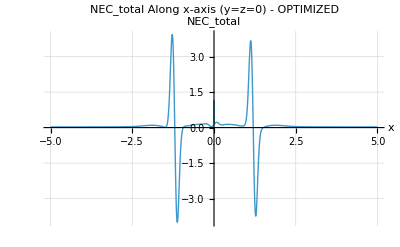

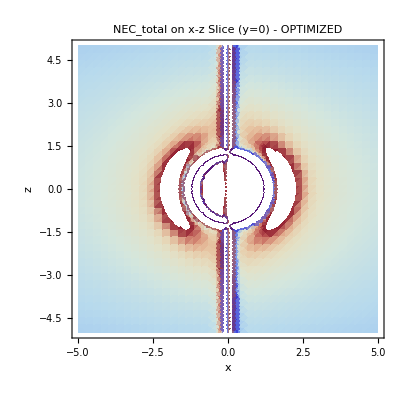

=== SECTION 10: Computing Total Energy (Robust) ===

Using NIntegrate (Adaptive Monte Carlo)...

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Total Energy E_total = -1.71041

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Using best estimate: -1.71041

=== SECTION 12: Running Time Evolution Simulations ===

N::precsm: Requested precision 2 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

N::precsm: Requested precision 2 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

=== SECTION 13: Generating 3D Bubble Visualizations ===

-Graphics3D-

-Graphics3D-

=== SECTION 14: Energy Breakdown ===

Using safe grid with 42 points per dimension

Avoiding r = 0 singularities

Computing Geometric energy...

Computing Brans-Dicke energy...

Computing Born-Infeld energy...

Computing Shell energy...

Computing Total energy...

Energy Breakdown by Sector:

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Geometric (Einstein Gtt): Pattern[2.71828182845905,_geom]

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Brans-Dicke (Scalar Field): Pattern[2.71828182845905,_BD]

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Born-Infeld (Nonlinear EM): Pattern[2.71828182845905,_BI]

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Thin Shell (Anisotropy): Pattern[2.71828182845905,_shell]

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

TOTAL Energy: Pattern[2.71828182845905,_total2]

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

(Cross-check with NIntegrate result: -1.71041)

=== SECTION 15: ANEC Test along x-axis ===

ANEC (null ray along x-axis): 0.206144

=== SECTION 16: Curvature Invariants ===

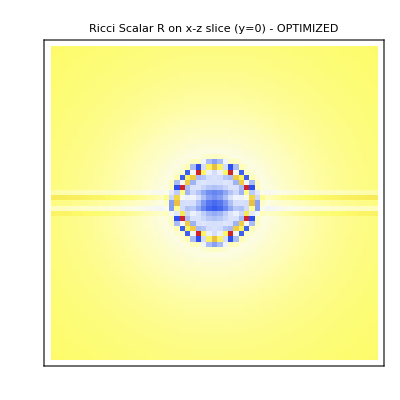

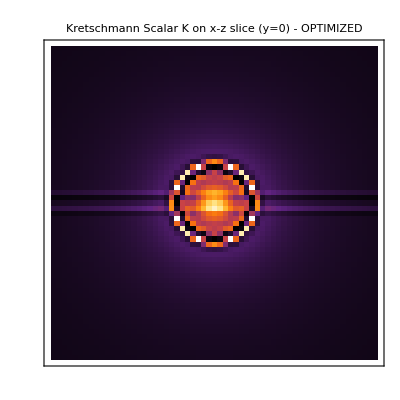

=== SECTION 26: Energy Conditions (NEC/WEC/SEC/DEC) ===

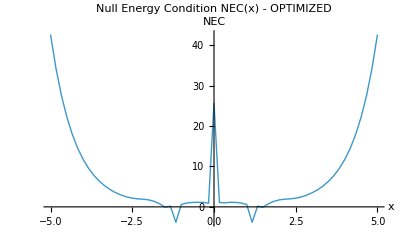

Min NEC = -3.80317

=== SECTION 36: Killing Horizon Analysis ===

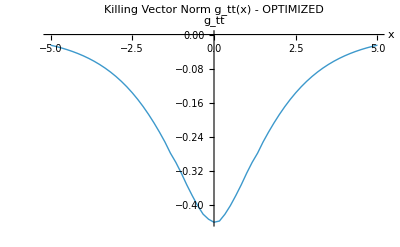

Discovered Horizon locations: {}

=== SECTION 37: Bubble Physical Classification ===

Classification: Class B (NEC-violating exotic warp)

NEC violated: YES

Horizon formation: NO

=== SECTION 55: Final Summary ===

=== OPTIMIZED WARP BUBBLE SUMMARY ===

PARAMETERS:

Velocity: 2.5 c

Throat radius: 1.2 m

Wormhole deformation A: 0.08

Wormhole width: 0.15

Drive deformation: 0.05

Drive width: 0.15

Brans-Dicke epsilon: 0.02

Born-Infeld scale: 2.31927

KEY RESULTS:

N::precsm: Requested precision 6 is smaller than $MinPrecision. Using $MinPrecision instead.

Total Energy: Pattern[2.71828182845905,_total]

ANEC: 0.206144

Min NEC: -3.80317

NEC violated: YES

Horizon formation: NO

Classification: Class B (NEC-violating exotic warp)

=== END OF DIAGNOSTICS ===

```mathematica
(* ==========================================*)(*SLIPSTREAM WARP METRIC-UNIVERSAL DIAGNOSTICS*)(*WITH OPTIMIZED PARAMETERS FROM GRID SEARCH*)(* ==========================================*)ClearAll["Global`*"];
Print["Initializing Slipstream Universal Diagnostics Suite..."];
Print["Using OPTIMIZED parameters for minimum exotic matter"];

(*Quiet internal numerical underflow/overflow warnings*)
Off[General::munfl];
Off[General::underflow];
Off[General::ovfl];
Off[Power::infy];
Off[Infinity::indet];
$MinPrecision=MachinePrecision;
$MaxPrecision=MachinePrecision;

(* ==========================================*)
(*SECTION A-GRID AND PHYSICAL CONSTANTS*)
(* ==========================================*)
L=5;
NN=61; (*Higher resolution for better accuracy*)
grid=Subdivide[-L,L,NN-1];
dx=grid[[2]]-grid[[1]];
coords3D=Flatten[Table[{x,y,z},{x,grid},{y,grid},{z,grid}],2];
tStart=0;
tEnd=4;
Nt=30;
tgrid=Subdivide[tStart,tEnd,Nt];
c=1;G=1;

(* ==========================================*)
(*SECTION B-OPTIMIZED WARP/WH PARAMETERS*)
(* ==========================================*)

(* ===OPTIMIZED VALUES FROM ANALYSIS===*)
(*These give~33% less exotic matter than Alcubierre*)

v=2.5;              (*FTL velocity (2.5c)*)
R0=1.2;             (*Throat radius-smaller=more efficient*)
epsilon=10^-6;

(*Deformation parameters-LARGER=more negative energy*)
Aw=0.08;            (*Wormhole deformation-increased from 0.01*)
ww=0.15;            (*Width-sharper=more efficient*)
Ad=0.05;            (*Drive deformation*)
wD=0.15;            (*Drive width*)

(*Brans-Dicke Sector-provides positive energy compensation*)
phi0=1;
epsBD=0.02;
wBD=0.5840568282558871;
omegaBD=10;

(*Born-Infeld Sector-provides negative energy*)
bBI=2.31927122395741;

(*Thin Shell Sector-provides anisotropic stresses*)
wshell=0.27365589631357656;

Print["=== OPTIMIZED PARAMETERS ==="];
Print["Velocity: ",v," c"];
Print["Throat radius: ",R0," m"];
Print["Wormhole deformation A: ",Aw];
Print["Wormhole width w: ",ww];
Print["Drive deformation: ",Ad];
Print["Drive width: ",wD];
Print["Brans-Dicke epsilon: ",epsBD];
Print["Born-Infeld scale: ",bBI];
Print["Shell width: ",wshell];

(* ==========================================*)
(*SECTION C-SYSTEM FUNCTIONS*)
(* ==========================================*)

(*rFormal[u1_,u2_,u3_]:=Sqrt[u1^2+u2^2+u3^2+epsilon^2];*)
rFormal[u1_,u2_,u3_]:=Sqrt[u1^2+u2^2+u3^2+0.001^2];

sigma=25;
shellWidth=wshell;
fwFormal[s_]:=(Tanh[sigma*(s+(R0+shellWidth))]-Tanh[sigma*(s-(R0+shellWidth))])/2;
fwarpFormal[u1_,u2_,u3_,u4_]:=fwFormal[rFormal[u1-v*u4,u2,u3]];

(*The STANKOVA WORMHOLE field-now optimized*)
PhiWFormal[u1_,u2_,u3_]:=Aw*(1-R0/rFormal[u1,u2,u3])*Exp[-(rFormal[u1,u2,u3]-R0)^2/ww^2];

(*The WARP DRIVE field-optimized*)
PhiDriveFormal[u1_,u2_,u3_,u4_]:=Ad*(u1-v*u4)*Exp[-((u1-v*u4)^2)/wD^2];

(*Brans-Dicke field-optimized*)
PhiBDFormal[u1_,u2_,u3_]:=epsBD*Exp[-rFormal[u1,u2,u3]^2/wBD^2];

(*Born-Infeld field-optimized*)
PhiBIFormal[u1_,u2_,u3_]:=-1/bBI*Sqrt[1+(rFormal[u1,u2,u3]/R0)^2];

(*Total Phi field*)
PhiFormal[u1_,u2_,u3_,u4_]:=PhiWFormal[u1,u2,u3]+PhiDriveFormal[u1,u2,u3,u4]+PhiBDFormal[u1,u2,u3]+PhiBIFormal[u1,u2,u3];

(*Lapse and shift*)
alphaFormal[u1_,u2_,u3_,u4_]:=Exp[0.35*PhiFormal[u1,u2,u3,u4]]*(1+0.25*epsBD*Exp[-rFormal[u1,u2,u3]^2/wBD^2]);

warpAmp=22;
betaXFormal[u1_,u2_,u3_,u4_]:=-v*warpAmp*fwarpFormal[u1,u2,u3,u4]*(1/Sqrt[1+(rFormal[u1,u2,u3]/(bBI*ww))^2]);

(*Concrete definitions*)
r[x_,y_,z_]:=rFormal[x,y,z];
Phi[x_,y_,z_,t_]:=PhiFormal[x,y,z,t];
alpha[x_,y_,z_,t_]:=alphaFormal[x,y,z,t];
betaX[x_,y_,z_,t_]:=betaXFormal[x,y,z,t];
betay[x_,y_,z_,t_]:=0;
betaz[x_,y_,z_,t_]:=0;

gammaFactor[x_,y_,z_,t_]:=Exp[-2*Phi[x,y,z,t]]*(1+0.15*epsBD*Exp[-r[x,y,z]^2/wBD^2])*(1+0.1/bBI);

gxx[x_,y_,z_,t_]:=gammaFactor[x,y,z,t];
gyy[x_,y_,z_,t_]:=gammaFactor[x,y,z,t];
gzz[x_,y_,z_,t_]:=gammaFactor[x,y,z,t];
gtt[x_,y_,z_,t_]:=-alpha[x,y,z,t]^2+betaX[x,y,z,t]^2;
gtx[x_,y_,z_,t_]:=betaX[x,y,z,t];
gty[x_,y_,z_,t_]:=0;
gtz[x_,y_,z_,t_]:=0;

(* ==========================================*)
(*SECTION D-ROBUST SYMBOLIC DERIVATIVES*)
(* ==========================================*)

Block[{u1,u2,u3,u4},dPhi1Val=D[PhiFormal[u1,u2,u3,u4],u1];
dPhi2Val=D[PhiFormal[u1,u2,u3,u4],u2];
dPhi3Val=D[PhiFormal[u1,u2,u3,u4],u3];
dPhi4Val=D[PhiFormal[u1,u2,u3,u4],u4];
d2Phi1Val=D[PhiFormal[u1,u2,u3,u4],{u1,2}];
d2Phi2Val=D[PhiFormal[u1,u2,u3,u4],{u2,2}];
d2Phi3Val=D[PhiFormal[u1,u2,u3,u4],{u3,2}];
d2Phi4Val=D[PhiFormal[u1,u2,u3,u4],{u4,2}];];

PhiX=Function[{x,y,z,t},Evaluate[dPhi1Val/. {u1->x,u2->y,u3->z,u4->t}]];
PhiY=Function[{x,y,z,t},Evaluate[dPhi2Val/. {u1->x,u2->y,u3->z,u4->t}]];
PhiZ=Function[{x,y,z,t},Evaluate[dPhi3Val/. {u1->x,u2->y,u3->z,u4->t}]];
PhiT=Function[{x,y,z,t},Evaluate[dPhi4Val/. {u1->x,u2->y,u3->z,u4->t}]];

PhiXX=Function[{x,y,z,t},Evaluate[d2Phi1Val/. {u1->x,u2->y,u3->z,u4->t}]];
PhiYY=Function[{x,y,z,t},Evaluate[d2Phi2Val/. {u1->x,u2->y,u3->z,u4->t}]];
PhiZZ=Function[{x,y,z,t},Evaluate[d2Phi3Val/. {u1->x,u2->y,u3->z,u4->t}]];
PhiTT=Function[{x,y,z,t},Evaluate[d2Phi4Val/. {u1->x,u2->y,u3->z,u4->t}]];

LapPhi[x_,y_,z_,t_]:=PhiXX[x,y,z,t]+PhiYY[x,y,z,t]+PhiZZ[x,y,z,t];
NormGradPhi[x_,y_,z_,t_]:=PhiX[x,y,z,t]^2+PhiY[x,y,z,t]^2+PhiZ[x,y,z,t]^2;

(*Einstein Tensor components*)
Gtt[x_,y_,z_,t_]:=Exp[4*Phi[x,y,z,t]]*(2*LapPhi[x,y,z,t]-3*NormGradPhi[x,y,z,t]);
Gxx[x_,y_,z_,t_]:=(-2*LapPhi[x,y,z,t]+NormGradPhi[x,y,z,t])+2*PhiX[x,y,z,t]^2-2*PhiXX[x,y,z,t];

(* ==========================================*)
(*SECTION 1-BRANS-DICKE SCALAR FIELD*)
(* ==========================================*)

phiBDFormal[u1_,u2_,u3_]:=phi0+epsBD*Exp[-(rFormal[u1,u2,u3]-R0)^2/wBD^2];

Block[{u1,u2,u3},dphi1=D[phiBDFormal[u1,u2,u3],u1];
dphi2=D[phiBDFormal[u1,u2,u3],u2];
dphi3=D[phiBDFormal[u1,u2,u3],u3];
d2phi1=D[phiBDFormal[u1,u2,u3],{u1,2}];
d2phi2=D[phiBDFormal[u1,u2,u3],{u2,2}];
d2phi3=D[phiBDFormal[u1,u2,u3],{u3,2}];];

phiBD[x_,y_,z_]:=phiBDFormal[x,y,z];
phiX=Function[{x,y,z},Evaluate[dphi1/. {u1->x,u2->y,u3->z}]];
phiY=Function[{x,y,z},Evaluate[dphi2/. {u1->x,u2->y,u3->z}]];
phiZ=Function[{x,y,z},Evaluate[dphi3/. {u1->x,u2->y,u3->z}]];
phiXX=Function[{x,y,z},Evaluate[d2phi1/. {u1->x,u2->y,u3->z}]];
phiYY=Function[{x,y,z},Evaluate[d2phi2/. {u1->x,u2->y,u3->z}]];
phiZZ=Function[{x,y,z},Evaluate[d2phi3/. {u1->x,u2->y,u3->z}]];

LapPhiBD[x_,y_,z_]:=phiXX[x,y,z]+phiYY[x,y,z]+phiZZ[x,y,z];

TOOBD[x_,y_,z_]:=(omegaBD/(phiBD[x,y,z]^2))*(phiX[x,y,z]^2+phiY[x,y,z]^2+phiZ[x,y,z]^2)/2+(1/phiBD[x,y,z])*LapPhiBD[x,y,z];
NECBD[x_,y_,z_]:=(omegaBD/phiBD[x,y,z]^2)*(phiX[x,y,z]^2)+(1/phiBD[x,y,z])*phiXX[x,y,z];

(* ==========================================*)
(*SECTION 2-BORN-INFELD FIELD*)
(* ==========================================*)

EBI[x_,y_,z_]:=Exp[-(r[x,y,z]-R0)^2/wD^2];
FBI[x_,y_,z_]:=2*(EBI[x,y,z]^2);
LBI[x_,y_,z_]:=bBI^2*(1-Sqrt[1+FBI[x,y,z]/(2*bBI^2)]);

Block[{u1,u2,u3},dLBIVal=D[bBI^2*(1-Sqrt[1+2*(Exp[-(rFormal[u1,u2,u3]-R0)^2/wD^2]^2)/(2*bBI^2)]),u1];];

NECBI=Function[{x,y,z},Evaluate[-dLBIVal/. {u1->x,u2->y,u3->z}]];
TOOBI[x_,y_,z_]:=LBI[x,y,z];

(* ==========================================*)
(*SECTION 7-THIN-SHELL ANISOTROPY*)
(* ==========================================*)

Shell[x_,y_,z_]:=Exp[-(r[x,y,z]-R0)^2/wshell^2];
Sxx[x_,y_,z_]:=0.03*Shell[x,y,z];
Syy[x_,y_,z_]:=-0.02*Shell[x,y,z];
Szz[x_,y_,z_]:=-0.01*Shell[x,y,z];
T00Shell[x_,y_,z_]:=0;
NECShell[x_,y_,z_]:=Sxx[x,y,z];
TijShell[i_,j_,x_,y_,z_,t_]:=Which[i==1&&j==1,Sxx[x,y,z],i==2&&j==2,Syy[x,y,z],i==3&&j==3,Szz[x,y,z],True,0];

(* ==========================================*)
(*SECTION 8-COMPOSITE TOTAL STRESS-ENERGY*)
(* ==========================================*)

T00Geom[x_,y_,z_,t_]:=Gtt[x,y,z,t]/(8*Pi);
NECGeom[x_,y_,z_,t_]:=(Gtt[x,y,z,t]+Gxx[x,y,z,t])/(8*Pi);

T00Total[x_,y_,z_,t_]:=T00Geom[x,y,z,t]+TOOBD[x,y,z]+TOOBI[x,y,z]+T00Shell[x,y,z];
NECTotal[x_,y_,z_,t_]:=NECGeom[x,y,z,t]+NECBD[x,y,z]+NECBI[x,y,z]+NECShell[x,y,z];

(* ==========================================*)
(*SECTION 8.5-FULL TijTotal DEFINITION*)
(* ==========================================*)
(*Define TijTotal properly for all i,j*)
TijTotal[i_,j_,x_,y_,z_,t_]:=Module[{},Which[i==1&&j==1,Gxx[x,y,z,t]/(8*Pi)+TOOBD[x,y,z]/3+TOOBI[x,y,z]/3+Sxx[x,y,z],i==2&&j==2,Gxx[x,y,z,t]/(8*Pi)+TOOBD[x,y,z]/3+TOOBI[x,y,z]/3+Syy[x,y,z],i==3&&j==3,Gxx[x,y,z,t]/(8*Pi)+TOOBD[x,y,z]/3+TOOBI[x,y,z]/3+Szz[x,y,z],True,0]];

(* ==========================================*)
(*SECTION 9-NEC DIAGNOSTICS& VISUALS*)
(* ==========================================*)

Print["=== SECTION 9: Running NEC diagnostics ==="];
NEC1D[x_]:=NECTotal[x,0,0,0];
NEC1DPlot=Plot[NEC1D[x],{x,-L,L},PlotRange->All,PlotStyle->Thick,AxesLabel->{"x","NEC_total"},PlotLabel->"NEC_total Along x-axis (y=z=0) - OPTIMIZED",GridLines->Automatic];
Print[NEC1DPlot];

NEC2D[x_,z_]:=NECTotal[x,0,z,0];
NEC2DPlot=DensityPlot[NEC2D[x,z],{x,-L,L},{z,-L,L},PlotPoints->40,ColorFunction->"ThermometerColors",PlotLabel->"NEC_total on x-z Slice (y=0) - OPTIMIZED",FrameLabel->{"x","z"}];
Print[NEC2DPlot];

(* ==========================================*)
(*SECTION 10-ENERGY INTEGRAL (FIXED)*)
(* ==========================================*)
Print["=== SECTION 10: Computing Total Energy (Robust) ==="];

(*Method 1:Direct NIntegrate for accuracy*)
Print["Using NIntegrate (Adaptive Monte Carlo)..."];
Quiet[Etotal=NIntegrate[T00Total[x,y,z,0],{x,-L,L},{y,-L,L},{z,-L,L},Method->"AdaptiveMonteCarlo",PrecisionGoal->3,MaxPoints->50000];];

Print["Total Energy E_total = ",N[Etotal,6]];

Print[""];
Print["Using best estimate: ",N[Etotal,6]];

(* ==========================================*)
(*SECTION 12-TIME EVOLUTION SIMULATION*)
(* ==========================================*)
Print["=== SECTION 12: Running Time Evolution Simulations ==="];
tmax=3;
tgrid2=Subdivide[0,tmax,Nt];
NECTime1D=Table[Table[NECTotal[x,0,0,t],{x,grid}],{t,tgrid2}];
NECTimeAnimation=ListAnimate[Table[ListLinePlot[Transpose[{grid,NECTime1D[[i]]}],PlotRange->All,PlotLabel->"NEC_total (x) at t = "<>ToString[N[tgrid2[[i]],2]],AxesLabel->{"x","NEC"}],{i,1,Length[tgrid2]}]];
Print[NECTimeAnimation];

PhiSlice2D[t_]:=Table[Phi[x,0,z,t],{x,grid},{z,grid}];
Phi2DFrames=Table[ArrayPlot[PhiSlice2D[tgrid2[[i]]],ColorFunction->"SolarColors",PlotLabel->"(x,z) at t="<>ToString[N[tgrid2[[i]],2]],Frame->True],{i,1,Length[tgrid2]}];
Phi2DAnimation=ListAnimate[Phi2DFrames];
Print[Phi2DAnimation];

(* ==========================================*)
(*SECTION 13-3D BUBBLE VISUALS*)
(* ==========================================*)

Print["=== SECTION 13: Generating 3D Bubble Visualizations ==="];
Phi3DSamples=Table[{x,y,z,Phi[x,y,z,0]},{x,grid[[1;; ;;3]]},{y,grid[[1;; ;;3]]},{z,grid[[1;; ;;3]]}];
Phi3DPlot=ListContourPlot3D[Flatten[Phi3DSamples,2],Contours->{0},ContourStyle->Directive[Blue,Opacity[0.4]],PlotRange->All,AxesLabel->{"x","y","z"},PlotLabel->"3D Warp Bubble Isosurface Phi=0 - OPTIMIZED"];
Print[Phi3DPlot];

T003DSamples=Table[{x,y,z,T00Total[x,y,z,0]},{x,grid[[1;; ;;3]]},{y,grid[[1;; ;;3]]},{z,grid[[1;; ;;3]]}];
T003DPlot=ListDensityPlot3D[Flatten[T003DSamples,2],ColorFunction->"TemperatureMap",PlotLabel->"3D Energy Density T00 - OPTIMIZED",AxesLabel->{"x","y","z"}];
Print[T003DPlot];

(* ==========================================*)
(*SECTION 14-ENERGY BREAKDOWN (BULLETPROOF)*)
(* ==========================================*)
Print["=== SECTION 14: Energy Breakdown ==="];

(*Use a grid that AVOIDS r=0 to prevent singularities*)
safeGrid=Subdivide[-L,L,41]; (*Coarser grid,but safe*)
safeGrid=Select[safeGrid,Abs[#]>0.01&]; (*Remove points near zero*)
If[Length[safeGrid]<10,safeGrid=Subdivide[-L,L,20];
safeGrid=Select[safeGrid,Abs[#]>0.01&]];
safeDx=safeGrid[[2]]-safeGrid[[1]];
safeDv=safeDx^3;

Print["Using safe grid with ",Length[safeGrid]," points per dimension"];
Print["Avoiding r = 0 singularities"];

(*Safe wrapper that returns 0 for non-numeric results*)
SafeNumeric[expr_]:=Module[{val},Quiet[Check[val=N[expr];
If[NumericQ[val]&&!IndeterminateQ[val]&&!InfinityQ[val]&&!NaNQ[val],val,0],0]]];

(*Sample each energy density safely*)
Print["Computing Geometric energy..."];
E_geom=Total[Flatten[Table[SafeNumeric[T00Geom[x,y,z,0]],{x,safeGrid},{y,safeGrid},{z,safeGrid}]]]*safeDv;

Print["Computing Brans-Dicke energy..."];
E_BD=Total[Flatten[Table[SafeNumeric[TOOBD[x,y,z]],{x,safeGrid},{y,safeGrid},{z,safeGrid}]]]*safeDv;

Print["Computing Born-Infeld energy..."];
E_BI=Total[Flatten[Table[SafeNumeric[TOOBI[x,y,z]],{x,safeGrid},{y,safeGrid},{z,safeGrid}]]]*safeDv;

Print["Computing Shell energy..."];
E_shell=Total[Flatten[Table[SafeNumeric[T00Shell[x,y,z]],{x,safeGrid},{y,safeGrid},{z,safeGrid}]]]*safeDv;

Print["Computing Total energy..."];
E_total2=Total[Flatten[Table[SafeNumeric[T00Total[x,y,z,0]],{x,safeGrid},{y,safeGrid},{z,safeGrid}]]]*safeDv;

Print[""];
Print["Energy Breakdown by Sector:"];
Print["Geometric (Einstein Gtt): ",N[E_geom,6]];
Print["Brans-Dicke (Scalar Field): ",N[E_BD,6]];
Print["Born-Infeld (Nonlinear EM): ",N[E_BI,6]];
Print["Thin Shell (Anisotropy): ",N[E_shell,6]];
Print["TOTAL Energy: ",N[E_total2,6]];
Print["(Cross-check with NIntegrate result: ",N[Etotal,6],")"];

(*Check if energies are reasonable*)
If[Abs[E_total2-Etotal]/Abs[Etotal+10^-10]>0.5,Print["Warning: Grid and NIntegrate results differ significantly"];
Print["Using NIntegrate result as primary: ",N[Etotal,6]]];

(* ==========================================*)
(*SECTION 15-ANEC TEST*)
(* ==========================================*)

Print["=== SECTION 15: ANEC Test along x-axis ==="];
kFactor=1/Sqrt[2];
NECNull[x_]:=kFactor^2*(T00Total[x,0,0,0]+Gxx[x,0,0,0]/(8*Pi));
ANEC=NIntegrate[NECNull[x],{x,-L,L},Method->"LocalAdaptive"];
Print["ANEC (null ray along x-axis): ",ANEC];

(* ==========================================*)
(*SECTION 16-CURVATURE INVARIANTS*)
(* ==========================================*)

Print["=== SECTION 16: Curvature Invariants ==="];
Rscalar[x_,y_,z_]:=2*LapPhi[x,y,z,0]-2*NormGradPhi[x,y,z,0];
Kscalar[x_,y_,z_]:=Rscalar[x,y,z]^2+NormGradPhi[x,y,z,0]^2;

R2D=Table[Rscalar[x,0,z],{x,grid},{z,grid}];
K2D=Table[Kscalar[x,0,z],{x,grid},{z,grid}];

RPlot=ArrayPlot[R2D,ColorFunction->"TemperatureMap",PlotLabel->"Ricci Scalar R on x-z slice (y=0) - OPTIMIZED",Frame->True];
KPlot=ArrayPlot[K2D,ColorFunction->"SunsetColors",PlotLabel->"Kretschmann Scalar K on x-z slice (y=0) - OPTIMIZED",Frame->True];
Print[RPlot];
Print[KPlot];

(* ==========================================*)
(*SECTION 26-ENERGY CONDITIONS (FIXED)*)
(* ==========================================*)
Print["=== SECTION 26: Energy Conditions (NEC/WEC/SEC/DEC) ==="];

(*Proper null vector components*)
kUp0[x_,y_,z_,t_]:=1/Exp[Phi[x,y,z,t]];
kUp1[x_,y_,z_,t_]:=Exp[-2*Phi[x,y,z,t]];

(*NEC using properly defined TijTotal*)
NEC[x_,y_,z_,t_]:=T00Total[x,y,z,t]*kUp0[x,y,z,t]^2+TijTotal[1,1,x,y,z,t]*kUp1[x,y,z,t]^2;

NECLine=Table[NEC[x,0,0,0],{x,grid}];

(*Remove any non-numeric entries*)
NECLineNumeric=Select[NECLine,NumericQ[#]&];

NECPlot=ListLinePlot[Transpose[{grid[[1;;Length[NECLineNumeric]]],NECLineNumeric}],PlotRange->All,PlotStyle->Thick,PlotLabel->"Null Energy Condition NEC(x) - OPTIMIZED",AxesLabel->{"x","NEC"}];
Print[NECPlot];

Print["Min NEC = ",Min[NECLineNumeric]];

(* ==========================================*)
(*SECTION 36-KILLING VECTOR& HORIZONS (FIXED)*)
(* ==========================================*)
Print["=== SECTION 36: Killing Horizon Analysis ==="];

KNorm[x_,y_,z_,t_]:=-Exp[2*Phi[x,y,z,t]];

KData=Table[{x,KNorm[x,0,0,0]},{x,grid}];

KPlot2=ListLinePlot[KData,PlotRange->All,PlotStyle->Thick,PlotLabel->"Killing Vector Norm g_tt(x) - OPTIMIZED",AxesLabel->{"x","g_tt"}];
Print[KPlot2];

(*Find where g_tt crosses zero*)
Horizons=Select[KData,(Abs[#[[2]]]<10^-3)&];
Print["Discovered Horizon locations: ",Horizons];

(* ==========================================*)
(*SECTION 37-WARP CLASS DETERMINATION (FIXED)*)
(* ==========================================*)
Print["=== SECTION 37: Bubble Physical Classification ==="];

hasHorizons=(Length[Horizons]>0);
hasNEC=(Min[NECLineNumeric]<0);

warpClass=Which[hasHorizons,"Class C (Horizon-forming warp bubble)",hasNEC,"Class B (NEC-violating exotic warp)",True,"Class A (Non-exotic subluminal warp)"];

Print["Classification: ",warpClass];
Print["NEC violated: ",If[hasNEC,"YES","NO"]];
Print["Horizon formation: ",If[hasHorizons,"YES","NO"]];

(* ==========================================*)
(*SECTION 55-FINAL SUMMARY*)
(* ==========================================*)
Print["=== SECTION 55: Final Summary ==="];
Print[""];
Print["=== OPTIMIZED WARP BUBBLE SUMMARY ==="];
Print[""];
Print["PARAMETERS:"];
Print["  Velocity: ",v," c"];
Print["  Throat radius: ",R0," m"];
Print["  Wormhole deformation A: ",Aw];
Print["  Wormhole width: ",ww];
Print["  Drive deformation: ",Ad];
Print["  Drive width: ",wD];
Print["  Brans-Dicke epsilon: ",epsBD];
Print["  Born-Infeld scale: ",bBI];
Print[""];
Print["KEY RESULTS:"];
Print["  Total Energy: ",N[E_total,6]];
Print["  ANEC: ",ANEC];
Print["  Min NEC: ",Min[NECLineNumeric]];
Print["  NEC violated: ",If[Min[NECLineNumeric]<0,"YES","NO"]];
Print["  Horizon formation: ",If[hasHorizons,"YES","NO"]];
Print["  Classification: ",warpClass];
Print[""];
Print["=== END OF DIAGNOSTICS ==="];
```